```mathematica
ClearAll["Global`*"]
```

Waveguide dimensions

```mathematica
w=0.12;
h=0.03;
l=0.15;
```

The magnetic field and electrode potentials

```mathematica
B=1;
Vu=1000;
Vd=0;
Vl=-500;
Vr=Vl;
```

Analytic method for the potential

```mathematica
nEnd=50;
fl[n_]=2/h Integrate[Vl Sin[n Pi/h y],{y,0,h}];
fr[n_]=2/h Integrate[Vr Sin[n Pi/h y],{y,0,h}];
ft[n_]=2/w Integrate[Vu Sin[n Pi/w x],{x,0,w}];
fb[n_]=2/w Integrate[Vd Sin[ n Pi/w x],{x,0,w}];
PotAnalytic=Evaluate[∑_(n=1)^nEnd (fl[n]Sin[(n Pi)/h(y+h/2)] Sinh[(n Pi)/h(w/2-x)]/Sinh[(n Pi)/h w]+fr[n]Sin[(n Pi)/h(y+h/2)] Sinh[(n Pi)/h(x+w/2)]/Sinh[(n Pi)/h w]+ ft[n]Sin[(n Pi)/w(x+w/2)] Sinh[(n Pi)/w(h/2-y)]/Sinh[(n Pi)/w h]+fb[n]Sin[(n Pi)/w(x+w/2)] Sinh[(n Pi)/w(y+h/2)]/Sinh[(n Pi)/w h])];
```

Numerical method for the potential

```mathematica
Ω= Rectangle[{-w/2,-h/2},{w/2,h/2}];
PotN=NDSolveValue[{∇_{x,y}^2 u[x,y]== 0,
DirichletCondition[u[x, y] == Vd,y == h/2 && -w/2 <= x <= w/2  ],
DirichletCondition[u[x, y] == Vu,y == -h/2 && -w/2 <= x <= w/2  ],
DirichletCondition[u[x, y] ==Vl, x==- w/2 && -h/2 <= y <= h/2 ],
DirichletCondition[u[x, y] ==Vr, x == w/2 && -h/2 <= y <= h/2 ]}, 
u, {x, y} ∈Ω,InterpolationOrder->All, MaxSteps->Infinity][x,y];
```

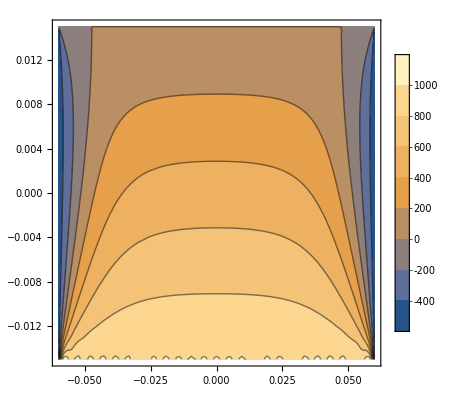
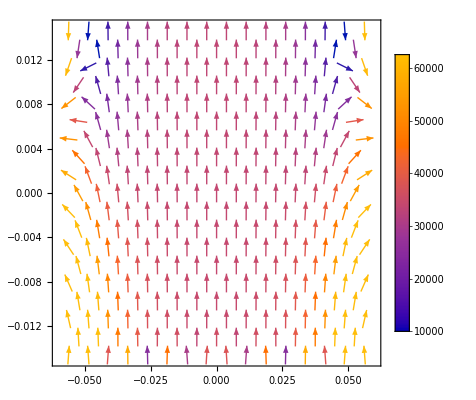
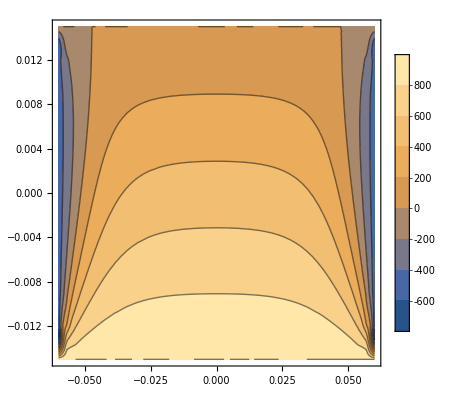
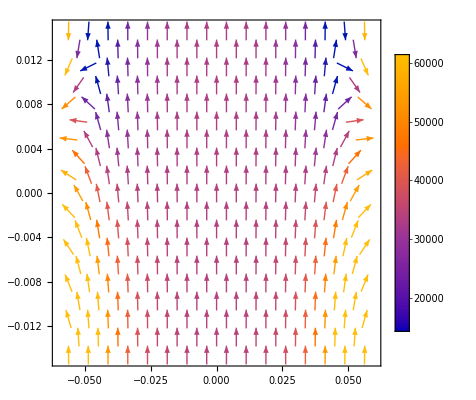

```mathematica
EfAnalytic = -Grad[PotAnalytic,{x,y}];
EfN= -Grad[PotN,{x,y}];
{ContourPlot[PotAnalytic,{x,-w/2,w/2},{y,-h/2,h/2},PlotLegends->Automatic],
VectorPlot[EfAnalytic,{x,-w/2,w/2},{y,-h/2,h/2},PlotLegends->Automatic],ContourPlot[PotN,{x,-w/2,w/2},{y,-h/2,h/2},PlotLegends->Automatic],
VectorPlot[EfN,{x,-w/2,w/2},{y,-h/2,h/2},PlotLegends->Automatic]}
```

Triangle Wave approximation

```mathematica
δ=10^-3;
trg =rb (1-2 ArcCos[(1-δ) Sin[2 π ωb t]]/π);
rs={trg,rc Sin[ωc t],rc Cos[ωc t]};
βs=D[rs,t]/c;
βsdot=D[βs,t];
```

```mathematica
ro={R0,0,0};
R=rs-ro;
ns=R/Sqrt[R.R];
```

```mathematica
Ek=18600;
me=511000;
c=299792458;
ϵ0=8.8541878128*10^-12;
γ=Ek/me+1;
β=Sqrt[1-1/γ^2];
e=1.60217663*10^-19;
ωc=B*c^2/(γ me);
rb=w/2;
θ=80*Pi/180;
R0=rb-.01;
ωb=β c Cos[θ]/rb;
rc=β c Sin[θ]/ωc;
Efield =Divide[-e,4Pi ϵ0 c]Cross[ns,Cross[ns-βs,βsdot]]//N;
```

One will want to to substitute t with tr before turning the fields into a list but we keep to plotting over tr

```mathematica
dt=10^-12;
tf=5*2Pi/ωb;
ExTable=Table[Efield[[1]],{t,0,tf,dt}];
EyTable=Table[Efield[[2]],{t,0,tf,dt}];
EzTable=Table[Efield[[3]],{t,0,tf,dt}];
sr=1/dt;
```

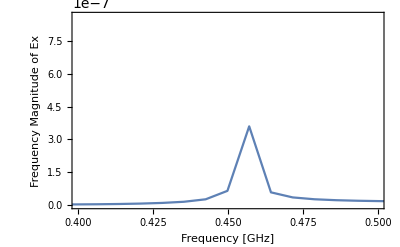

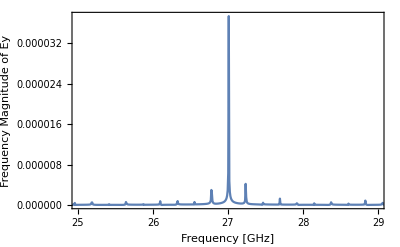

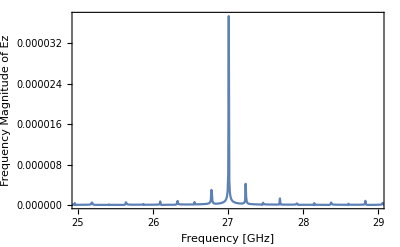

```mathematica
ftx=Fourier[ExTable,FourierParameters->{0,1}];
ff=(Table[(n-1) sr/Length[ExTable],{n,Length[ftx]}]//N)/10^9;
ListLinePlot[Transpose[{ff,Abs[ftx]}],PlotRange->{{.4,.5},All},Frame->True,FrameLabel->{"Frequency [GHz]","Frequency Magnitude of Ex"}]
fty=Fourier[EyTable,FourierParameters->{0,1}];
ListLinePlot[Transpose[{ff,Abs[fty]}],PlotRange->{{25,29},All},Frame->True,FrameLabel->{"Frequency [GHz]","Frequency Magnitude of Ey"}]
ftz=Fourier[EzTable,FourierParameters->{0,1}];
ListLinePlot[Transpose[{ff,Abs[ftz]}],PlotRange->{{25,29},All},Frame->True,FrameLabel->{"Frequency [GHz]","Frequency Magnitude of Ez"}]
```

Quartic potential

```mathematica
Vp=500;
pWidth=.02;
PerturbTerm[x_]=Vp(HeavisidePi[(x-w/2)/pWidth]);
nEnd=100;
Vs = Vl;
aterm[n_]=2/(w Sinh[n Pi h/w]) Integrate[(Vd+PerturbTerm[x]) Sin[n Pi/w x],{x,0,w}];
bterm[n_]=2/(w Sinh[n Pi h/w]) Integrate[(Vu +PerturbTerm[x]) Sin[n Pi/w x],{x,0,w}];
cterm[n_]=2/(h Sinh[n Pi w/h]) Integrate[Vs Sin[n Pi/h y],{y,0,h}];
VClosedForm[x_,y_]=∑_(n=1)^nEnd (Sin[n Pi x/w](aterm[n]Sinh[(n Pi)/w(h-y)] +bterm[n]Sinh[(n Pi)/w y] )+ cterm[n]*Sin[n Pi y/h](Sinh[(n Pi)/h(w-x)]+ Sinh[(n Pi)/h x]));
Ω= Rectangle[{0,0},{w,h}];
Vnum[x_,y_]=NDSolveValue[{∇_{x,y}^2 u[x,y]== 0,
DirichletCondition[u[x, y] == Vd,y == 0 && 0 <= x <=w/2-pWidth/2  ],
DirichletCondition[u[x, y] == Vd,y == 0 && w/2+pWidth/2 <= x <= w ],
DirichletCondition[u[x, y] == Vd+Vp,y == 0 && w/2-pWidth/2 <= x <=w/2+pWidth/2 ],
DirichletCondition[u[x, y] == Vu,y == h && 0<= x <=w/2-pWidth/2 ],
DirichletCondition[u[x, y] == Vu,y == h && w/2+pWidth/2 <= x <= w],
DirichletCondition[u[x, y] == Vu+Vp,y == h &&w/2-pWidth/2 <= x <=w/2+pWidth/2 ],
DirichletCondition[u[x, y] ==Vs, x==0 && 0 <= y <= h ],
DirichletCondition[u[x, y] ==Vs, x == w && 0 <= y <= h ]}, 
u, {x, y} ∈Ω,InterpolationOrder->All, MaxSteps->Infinity][x,y];
```

General::munfl: Csch[716.283] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Csch[728.849] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Csch[741.416] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

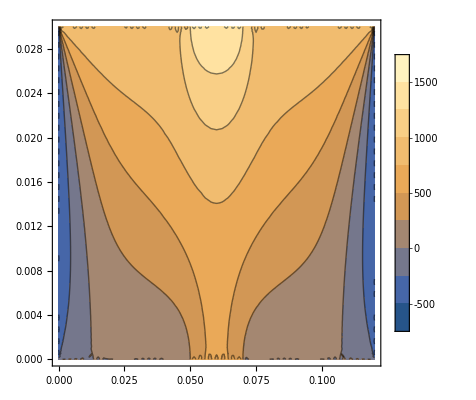
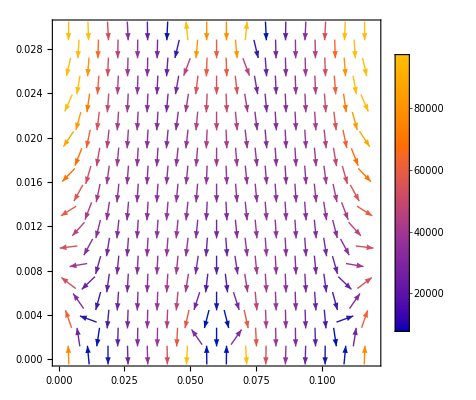

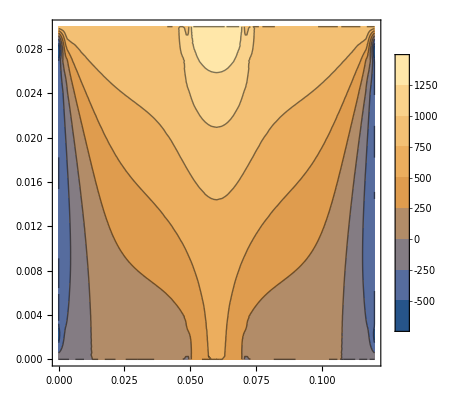
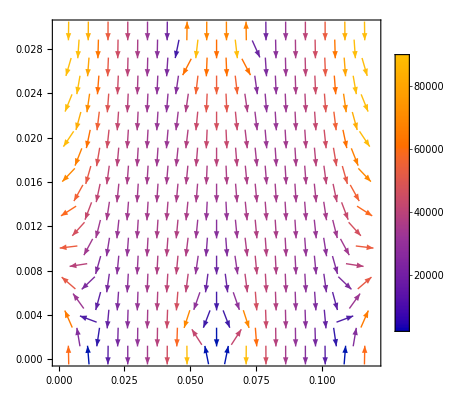

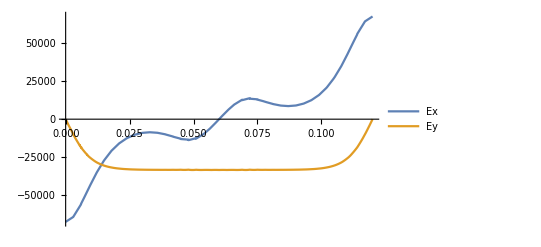

```mathematica
Eclosed[x_,y_] = -Grad[VClosedForm[x,y],{x,y}];
Enum[x_,y_] = -Grad[Vnum[x,y],{x,y}];
{ContourPlot[VClosedForm[x,y],{x,0,w},{y,0,h},PlotLegends->Automatic],
VectorPlot[Eclosed[x,y],{x,0,w},{y,0,h},PlotLegends->Automatic]}
{ContourPlot[Vnum[x,y],{x,0,w},{y,0,h},PlotLegends->Automatic],
VectorPlot[Enum[x,y],{x,0,w},{y,0,h},PlotLegends->Automatic]}
Plot[{Enum[x,h/2][[1]],Enum[x,h/2][[2]]},{x,0,w},PlotLegends->{"Ex","Ey"}]
```